## Načítanie dát

```mathematica
SetDirectory["C:\\Users\\student\\Harmaniak\\NMLA\\LU_rozklad\\"];

A=Import["matica.txt","Table"];
b=Import["ps.txt", "Table"];
xOriginal=Import["x.txt", "Table"];

Print["Matica A: ", A//MatrixForm]
Print["Pravá strana b: ", b//MatrixForm]
```

Matica A: (30. | -15. | 0. | -15. | 0. | 0. | 0. | 0. | 0.
-15. | 60. | 0. | 0. | -30. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
-15. | 0. | 0. | 60. | -30. | 0. | -15. | 0. | 0.
0. | -30. | 0. | -30. | 120. | 0. | 0. | -30. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | -15. | 0. | 0. | 30. | -15. | 0.
0. | 0. | 0. | 0. | -30. | 0. | -15. | 60. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

Pravá strana b: (416.667
1250.
50.
1250.
2500.
50.
833.333
1250.
50.)

## LU rozklad matice A

Iterácia 1: faktor rastu = 0.25

Iterácia 2: faktor rastu = 0.4375

Iterácia 3: faktor rastu = 0.4375

Iterácia 4: faktor rastu = 0.4375

Iterácia 5: faktor rastu = 0.666667

Iterácia 6: faktor rastu = 0.666667

Iterácia 7: faktor rastu = 0.666667

Iterácia 8: faktor rastu = 0.666667

Iterácia 9: faktor rastu = 0.666667

Dolná trojuholníková matica: (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 1 | 0 | 0 | 0 | 0 | 0 | 0
-0.5 | -0.142857 | 0. | 1 | 0 | 0 | 0 | 0 | 0
0. | -0.571429 | 0. | -0.666667 | 1 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 1 | 0 | 0 | 0
0. | 0. | 0. | -0.291667 | -0.125 | 0. | 1 | 0 | 0
0. | 0. | 0. | 0. | -0.375 | 0. | -0.769231 | 1 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1)

Horná trojuholníková matica: (30. | -15. | 0. | -15. | 0. | 0. | 0. | 0. | 0.
0. | 52.5 | 0. | -7.5 | -30. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 8.88178×10^-16 | 0. | 51.4286 | -34.2857 | 0. | -15. | 0. | 0.
0. | 3.55271×10^-15 | 0. | 0. | 80. | 0. | -10. | -30. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 7.03141×10^-16 | 0. | 1.77636×10^-15 | 0. | 0. | 24.375 | -18.75 | 0.
0. | 1.87315×10^-15 | 0. | 1.36643×10^-15 | 0. | 0. | 0. | 34.3269 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

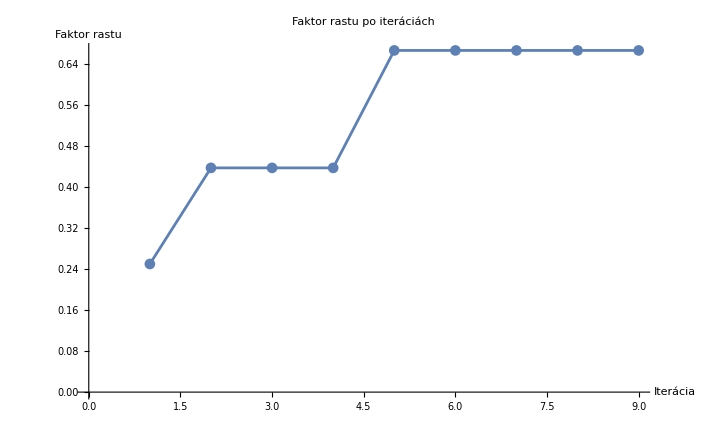

```mathematica
MyLUDecomposition[A_?MatrixQ]:=Module[{n,L,U,i,j,k,sum,growthFactors,maxA,currentMaxU,currentGrowthFactor},
n=Length[A];
L=ConstantArray[0,{n,n}];
U=ConstantArray[0,{n,n}];

growthFactors={};
maxA=Max[Abs[A]];

For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
sum=Sum[L[[i,k]] U[[k,j]],{k,1,i-1}];
U[[i,j]]=A[[i,j]]-sum;
];

L[[i,i]]=1;

For[j=i+1,j<=n,j++,
sum=Sum[L[[j,k]] U[[k,i]],{k,1,i-1}];
L[[j,i]]=(A[[j,i]]-sum)/U[[i,i]];
];

currentMaxU=Max[Abs[U]];
currentGrowthFactor=currentMaxU/maxA;
AppendTo[growthFactors,currentGrowthFactor];
Print["Iterácia ",i,": faktor rastu = ",currentGrowthFactor];
];

{L,U,growthFactors}
]

{L,U,growthFactors}=MyLUDecomposition[A];

Print["Dolná trojuholníková matica: ", L//MatrixForm]
Print["Horná trojuholníková matica: ", U//MatrixForm]

ListLinePlot[growthFactors,PlotMarkers->Automatic,PlotLabel->"Faktor rastu po iteráciách",AxesLabel->{"Iterácia","Faktor rastu"}]
```

## Riešenie Ax=b a počítanie chýb

```mathematica
ForwardSubstitution[L_,b_]:=Module[{n,y,i,sum},
n=Length[L];
y=ConstantArray[0,n];

For[i=1,i<=n,i++,
sum=Sum[L[[i,j]] y[[j]],{j,1,i-1}];
y[[i]]=b[[i]]-sum;
];

y
]

BackwardSubstitution[U_,y_]:=Module[{n,x,i,sum},
n=Length[U];
x=ConstantArray[0,n];

For[i=n,i>=1,i--,
sum=Sum[U[[i,j]] x[[j]],{j,i+1,n}];
x[[i]]=(y[[i]]-sum)/U[[i,i]];
];

x
]

y=ForwardSubstitution[L,b];
x=BackwardSubstitution[U,y];

Print["Porovnanie výsledkov x:"]
Print[x//MatrixForm , " = ",  xOriginal//MatrixForm]

Print["Ax = b:"]
Print[(A.x)//MatrixForm, " = ",b//MatrixForm]

r=b-A.x;
error=Norm[r];
relativeError=Norm[r]/(Norm[A]*Norm[x]);

Print["Chyba výpočtu: ", error]
Print["Relatívna chyba: ", relativeError]
```

Porovnanie výsledkov x:

(158.73
123.016
50.
166.667
125.
50.
174.603
126.984
50.) = (158.73
123.016
50.
166.667
125.
50.
174.603
126.984
50.)

Ax = b:

(416.667
1250.
50.
1250.
2500.
50.
833.333
1250.
50.) = (416.667
1250.
50.
1250.
2500.
50.
833.333
1250.
50.)

Chyba výpočtu: 1.65628×10^-12

Relatívna chyba: 2.94882×10^-17